```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[th1]:=Subscript[θ,1];Format[th2]:=Subscript[θ,2];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;
Format[Las]:=Subscript[Λ,s];Format[Lav]:=Subscript[Λ,v];Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
(*Format[al1]:=Subscript[α,1];Format[al2]:=Subscript[α,2];*)Format[siv]:=Subscript[σ,v];
Format[si1]:=Subscript[σ,1];Format[si2]:=Subscript[σ,2];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[y1]:=Subscript[y,1];Format[y2]:=Subscript[y,2];
Format[r1]:=Subscript[r,1];Format[r2]:=Subscript[r,2];
Format[c1]:=Subscript[c,1];Format[c2]:=Subscript[c,2];
(*Two-Strain Model with vaccination*)RNc={"s"+"i1"->2  "i1", "i1"-> "c1", "c1"-> "r1", "r1"+  "y2"->2  "y2",
"s"+"i2" ->2  "i2", "i2"-> "c2", "c2"-> "r2", "r2"+ "y1"->2"y1",
"s"+"y1" ->  "y1"+  "i1","s"+"y2" ->  "y2"+ "i2",
 "r1"+  "i2"-> "i2"+  "y2", "r2"+"i1"->"i1"+"y1","v"->"z","z"+"y2"-> 2"y2",
 "z"+ "i2"->  "i2"+  "y2", "y2"->"R", "y1"->"R"};
RN=Join[{0->"s",0->"v"},RNc,
{"s"->0,"i1" ->0,"c1" ->0,"r1" ->0,"y2" ->0,"i2" ->0,"c2" ->0,"r2" ->0,"y1" ->0,"v"->0,"z"->0,"R"->0}];
ks={ Las,Lav,be1,ga1,th1,si2 be2,be2,ga2,th2,si1 be1,be1,be2,si2 be2,si1 be1,
thv,siv be2,siv be2,ga2,ga1,mu,mu,mu,
mu,mu,mu,mu,mu,mu,mu,mu,mu};rts=mRts[RN,ks];
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
rts//Length
```

DFE::shdw: Symbol DFE appears in multiple contexts {EpidCRN`,Global`}; definitions in context EpidCRN` may shadow or be shadowed by other definitions.

Load CRNT

reactions and transitions: (0→s | Λ_s
0→v | Λ_v
i1+s→2 i1 | β_1 i_1 s
i1→c1 | γ_1 i_1
c1→r1 | c_1 θ_1
r1+y2→2 y2 | β_2 r_1 σ_2 y_2
i2+s→2 i2 | β_2 i_2 s
i2→c2 | γ_2 i_2
c2→r2 | c_2 θ_2
r2+y1→2 y1 | β_1 r_2 σ_1 y_1
s+y1→i1+y1 | β_1 s y_1
s+y2→i2+y2 | β_2 s y_2
i2+r1→i2+y2 | β_2 i_2 r_1 σ_2
i1+r2→i1+y1 | β_1 i_1 r_2 σ_1
v→z | θ_v v
y2+z→2 y2 | β_2 σ_v y_2 z
i2+z→i2+y2 | β_2 i_2 σ_v z
y2→R | γ_2 y_2
y1→R | γ_1 y_1
s→0 | μ s
i1→0 | i_1 μ
c1→0 | c_1 μ
r1→0 | μ r_1
y2→0 | μ y_2
i2→0 | i_2 μ
c2→0 | c_2 μ
r2→0 | μ r_2
y1→0 | μ y_1
v→0 | μ v
z→0 | μ z
R→0 | μ R)

31

```mathematica
(*Get bdAn outputs*)
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infV,ngm}=bdAn[RN,rts];
Print["r1,r2 are",R0A/.E0,"K=",K//MatrixForm," infV=",infV]
per={1,3,2,4};K[[per,per]]//MatrixForm
```

r1,r2 are{(β_1 Λ_s)/(μ (γ_1+μ)),(β_2 (Λ_s/μ+(Λ_v σ_v θ_v)/(μ (μ+θ_v))))/(γ_2+μ)}K=((β_1 s)/(γ_1+μ) | 0 | (β_1 s)/(γ_1+μ) | 0
0 | (β_2 s)/(γ_2+μ) | 0 | (β_2 s)/(γ_2+μ)
(β_1 r_2 σ_1)/(γ_1+μ) | 0 | (β_1 r_2 σ_1)/(γ_1+μ) | 0
0 | (β_2 (r_1 σ_2+σ_v z))/(γ_2+μ) | 0 | (β_2 (r_1 σ_2+σ_v z))/(γ_2+μ)) infV={i_1,i_2,y_1,y_2}

((β_1 s)/(γ_1+μ) | (β_1 s)/(γ_1+μ) | 0 | 0
(β_1 r_2 σ_1)/(γ_1+μ) | (β_1 r_2 σ_1)/(γ_1+μ) | 0 | 0
0 | 0 | (β_2 s)/(γ_2+μ) | (β_2 s)/(γ_2+μ)
0 | 0 | (β_2 (r_1 σ_2+σ_v z))/(γ_2+μ) | (β_2 (r_1 σ_2+σ_v z))/(γ_2+μ))

r1,r2 are

r1,r2 are

{(β_1 Λ_s)/(μ (γ_1+μ)),(β_2 (Λ_s/μ+(Λ_v σ_v θ_v)/(μ (μ+θ_v))))/(γ_2+μ)}

```mathematica
{E1,E2,r12,r21,coP,fl}=invNr[E1t,E2t,R0A,E0,par,cp,2,4]
```

Error: in2 must be an integer between 1 and 2

Set::shape: Lists {E1,E2,R12,R21,coP,fl} and $Failed are not the same shape.

$Failed

```mathematica
(*eq=Thread[(RHS/.coP)==0];
so=Solve[eq,var]//FullSimplify;
Print[so//Length," sols at nr. col coP, one is positive",so//N]
p0val=par/.coP;
pos=fpHopf[RHS, var, par, p0val]*)
```

```mathematica
plotInd={1,2};
steTol=10^(-8);
staTol=10^(-10);
choTol=10^(-13);

(*Call scan using all the precomputed values from memory*)
Timing[{fPl,unC,res}=scan[RHS,var,par,coP,plotInd,mSi,Automatic,steTol,staTol,choTol,R01,R02,r12,r21];]

fPl
```

Auto-determined varInd: {1,3,6}

Susceptible: S

Strain 1 (first compartment): I1

Strain 2 (first compartment): Y2

Computing R01=1, R02=1 intersection point...

R01-R02 intersection at: β_1 = 1.98242, β_2 = 1.18939

Adjusted ranges: β_1 ∈ [0.001, 5.97818], β_2 ∈ [0.001, 3.02311]

Scanning 121 parameter combinations...

Checked 30 potential coexistence points

All Rij equations: {0.504434 β_1==1,0.840767 β_2==1,(0.0690938 (3.50924+10.3983 β_1) β_2)/β_1==1,-1/β_20.564822 β_1 (-0.634221+15.1758 β_2-2.75027 √(0.946947 (3.70527-3.11527 β_2) β_2+(-0.230603+5.84265 β_2)^2))==1}

DFE: 16 (13%)

E2: 40 (33%)

E1: 35 (29%)

EE-Stable: 30 (25%)

{0.78125,Null}

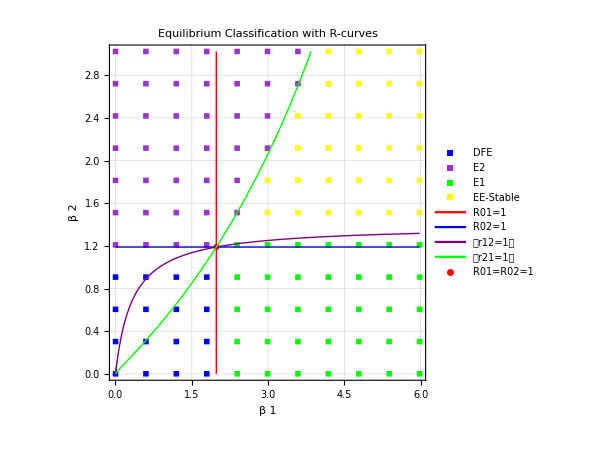

```mathematica
Export["BulhScan.pdf",fPl]
```

RahmanScan.pdf